```mathematica
f[x_]=E^(-x^2)
```

ⅇ^(-x^2)

```mathematica
h=0.1
```

0.1

```mathematica
apr=(f[0.1+h]-f[0.1-h])/(2h)
```

-0.196053

```mathematica
treci[x_]=D[f[x],{x,3}]
```

12 ⅇ^(-x^2) x-8 ⅇ^(-x^2) x^3

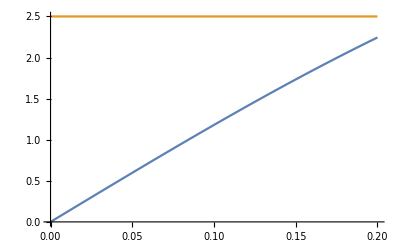

```mathematica
Plot[{treci[x],2.5},{x,0,0.2}]
```

```mathematica
m3=Abs[treci[0.2]]
```

2.2444

```mathematica
greska = m3/6 h^2
```

0.00374067

```mathematica
zad2[f_,x_,x0_,h_]:=Module[{},
((f/.x->(x0+h))-2(f/.x->x0) +(f/.x->(x0-h)))/h^2
]
```

```mathematica
zad2[E^(-x^2),x,0.1,0.1]
```

-1.93102

```mathematica
Table[zad2[E^(-x^2),x,0.1,10^-k],{k,1,15}]
```

{-1.93102,-1.9404,-1.9405,-1.9405,-1.9405,-1.94067,-1.94289,-3.33067,-111.022,-11102.2,-1.11022×10^6,-1.11022×10^8,-1.11022×10^10,-1.11022×10^12,-1.11022×10^14}

```mathematica
greska[f_,x_,x0_,h_]:=Module[{},
drugi=D[f,{x,2}];
ag=Abs[zad2[f,x,x0,h]-drugi/.x->x0];
rg=ag/Abs[drugi/.x->x0];
{ag,rg}
]
```

```mathematica
greska[E^(-t^2),t,0.1,10^-7]
```

{0.00239262,0.00123299}